# Section 5A

This is the first part of three notebooks in which the figures in Section 5 were created. To make any changes first Evaluate Initialization Cells.

## 3-dimensional analogue

Let’s make a pentagram

```mathematica
VPgm:=Table[{Cos[t],Sin[t]},{t,π/2,4π+π/2,(4π)/5}]
EPgm:=Table[Line[{VPgm[[i]],VPgm[[i+1]]}],{i,5}]
flagPgm:={VPgm[[2]],Midpoint[{VPgm[[2]],VPgm[[3]]}],{0,0}}
gphPgmedg:=Graphics[EPgm]
gphPgm:=Graphics[{Thick,EPgm,Opacity[1,Lighter[Darker[Yellow]]],Polygon[VPgm]}]
gphflagPgm:=Graphics[{PointSize[0.04],Point[flagPgm,VertexColors->{Red, Blue,Green}],Opacity[0.7,Cyan],ConvexHullMesh[flagPgm]}]
```

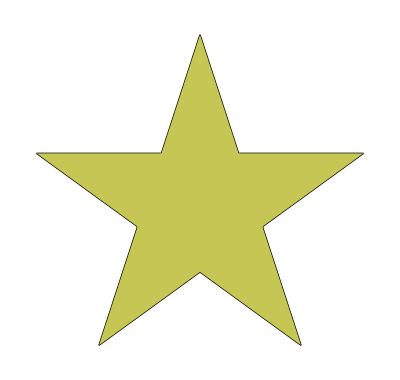

```mathematica
Show[gphPgm]
```

```mathematica
Graphics[{Black,EPgm,Blue,Line[{VPgm[[2]],VPgm[[3]]}],Magenta,PointSize[0.04],Point[flagPgm[[2]]+(Sqrt[5]-2)/2*(VPgm[[2]]-VPgm[[3]])]}];(*Here I find a vertex of the pentagon*)
```

Look at that pentagon in there:

```mathematica
u0:=flagPgm[[2]]+(Sqrt[5]-2)/2*(VPgm[[2]]-VPgm[[3]])
VPgn:=Table[RotationTransform[2*k*π/5][u0],{k,5}]
EPgn:=Table[Line[{VPgn[[i]],VPgn[[i+1]]}],{i,5}]
gphPgn:=Graphics[{Opacity[0.7,Blue],Polygon[VPgn]}]
```

gphP

```mathematica
Show[gphPgn,gphPgm]
```

-Graphics-

Can you imagine it is the vertex figure of some vertex in an icosahedron?

```mathematica
ico2:=Icosahedron[]
V2:=PolyhedronData["Icosahedron","VertexCoordinates"]
gphico2:=Graphics3D[{Opacity[0],ico2},Boxed->False]
gphedgPgm:=Graphics3D[{Thick,Line[{V2[[5]],V2[[11]],V2[[9]],V2[[3]],V2[[8]],V2[[10]],V2[[6]],V2[[4]],V2[[5]],V2[[9]],V2[[7]],V2[[3]],V2[[10]],V2[[12]],V2[[6]],V2[[5]]}]}]
verfig:={V2[[3]],V2[[5]],V2[[6]],V2[[9]],V2[[10]]}
gphvertfig:=Graphics3D[{Opacity[0.7,Blue],Polygon[{V2[[1]],V2[[3]],V2[[9]]}],Polygon[{V2[[1]],V2[[3]],V2[[10]]}],Polygon[{V2[[1]],V2[[5]],V2[[9]]}],Polygon[{V2[[1]],V2[[5]],V2[[6]]}],Polygon[{V2[[1]],V2[[6]],V2[[10]]}]}]
gphPgmico:=Graphics3D[{Opacity[0.7,Yellow],Polygon[{V2[[12]],V2[[6]],V2[[10]]}],Polygon[{V2[[4]],V2[[6]],V2[[5]]}],Polygon[{V2[[7]],V2[[9]],V2[[3]]}],Polygon[{V2[[8]],V2[[3]],V2[[10]]}],Polygon[{V2[[11]],V2[[5]],V2[[9]]}]}]
gphedgPgm:=Graphics3D[{Thick,Line[{V2[[5]],V2[[11]],V2[[9]],V2[[3]],V2[[8]],V2[[10]],V2[[6]],V2[[4]],V2[[5]],V2[[9]],V2[[7]],V2[[3]],V2[[10]],V2[[12]],V2[[6]],V2[[5]]}]}]
```

```mathematica
Show[gphico2,gphvertfig,gphedgPgm,gphPgmico]
```

-Graphics3D-

```mathematica
gphp1:=Graphics3D[{PointSize[0.04],Green,Point[V2[[12]]]}](*Here are the other vertices in the pentagon*)
gphp2:=Graphics3D[{PointSize[0.04],Blue,Point[V2[[3]]]}]
gphp3:=Graphics3D[{PointSize[0.04],Red,Point[V2[[5]]]}]
gphp4:=Graphics3D[{PointSize[0.04],Yellow,Point[V2[[6]]]}]
gphp5:=Graphics3D[{PointSize[0.04],Pink,Point[V2[[9]]]}]
gphp6:=Graphics3D[{PointSize[0.04],Purple,Point[V2[[10]]]}]
Show[gphico2,gphp1,gphp2,gphp3,gphp4,gphp5,gphp6,gphvertfig,gphedgPgm]
```

-Graphics3D-

Try to think of a flag that will generate that icosahedron:

```mathematica
flagPgnIco:={V2[[5]],Midpoint[{V2[[5]],V2[[9]]}],RegionCentroid[Polygon[{V2[[1]],V2[[5]],V2[[9]]}]],{0,0,0}}
gphflagPgnIco:=Graphics3D[{PointSize[0.04],Point[flagPgnIco,VertexColors->{Red, Blue,Green,Yellow}],Opacity[0.7,Magenta],ConvexHullMesh[flagPgnIco]}]
```

```mathematica
Show[gphico2,gphPgmico,gphvertfig,gphedgPgm,gphflagPgnIco]
```

-Graphics3D-

And how it would look in the 2D picture:

```mathematica
flagPgn:={u0,flagPgm[[2]],RegionCentroid[Polygon[{{0,0},u0,RotationTransform[2*1*π/5][u0]}]]}
gphflagPgn:=Graphics[{Line[{u0,flagPgm[[2]],RegionCentroid[Polygon[{{0,0},u0,RotationTransform[2*1*π/5][u0]}]],u0}],Opacity[0.7,Magenta],Polygon[flagPgn],PointSize[0.02],Point[flagPgn,VertexColors->{Red, Blue,Green}],}]
```

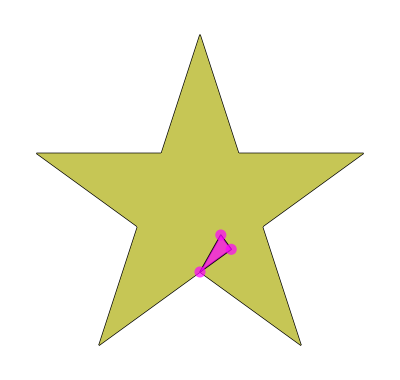

```mathematica
Show[gphPgn,gphPgm,gphflagPgn]
```

And a flag for the pentagram down there

```mathematica
flagPgm2:={VPgm[[2]],Midpoint[{VPgm[[2]],VPgm[[3]]}],{0,0}}
gphflagPgm2:=Graphics[{Line[{flagPgm2[[1]],flagPgm2[[2]],flagPgm2[[3]],flagPgm2[[1]]}],PointSize[0.02],Point[flagPgm2,VertexColors->{Red, Blue,Green}],Opacity[0.7,Cyan],ConvexHullMesh[flagPgm2]}]
```

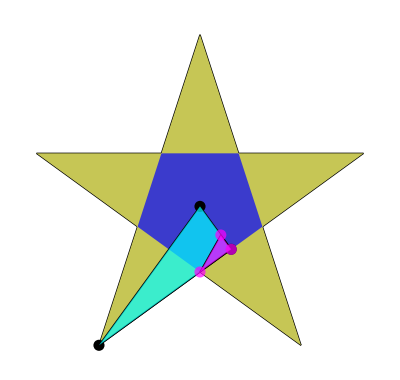

```mathematica
Show[gphPgm,gphPgn,gphflagPgm2,gphflagPgn]
```

And up there

```mathematica
flagPgmIco:={V2[[4]],flagPgnIco[[2]],V2[[1]],{0,0,0}}
gphflagPgmIco:=Graphics3D[{PointSize[0.04],Point[flagPgmIco,VertexColors->{Red, Blue,Green,Yellow}],Opacity[0.7,Cyan],ConvexHullMesh[flagPgmIco]}]
```

```mathematica
Show[gphico2,gphPgmico,gphvertfig,gphedgPgm,gphflagPgnIco,gphflagPgmIco]
```

-Graphics3D-

What happens if we make the icosahedron group defined by the purple flag act on the cyan flag?

Oops, that’s no regular polyhedron! What did we miss?
The base flag was not chosen correctly. This is what we call the naive flag in Section-5C.nb.
To find the correct flag by Wythoff’s construction much work was done.

First we define the linearizing function to work with the golden ratio without approximating every time (see Section-5C.nb):

```mathematica
Numerico=ρ->N[GoldenRatio];
```

```mathematica
LinealQ[p_]:=PolynomialQ[p,ρ]&&Exponent[p,ρ] <=1;
ReglaBaja[n_ ]:= ρ^n->ρ^(n-1)+ρ^(n-2)
```

```mathematica
HazLineal[pol_]:=Module[{p=pol},
		                                      If[PolynomialQ[p,ρ],
		                               While[Not[LinealQ[p]],
			          p=Collect[p/.ReglaBaja[Exponent[p,ρ] ],ρ]]; Expand[p],HazLineal/@pol]
			                                              ];
HazLineal[L_List]:=HazLineal/@L ;
```

And construct the icosahedron using the reflection matrices found in Wikipedia:

```mathematica
E2:={{-1,0,0},{0,1,0},{0,0,1}}
E1:=HazLineal[{{(1-ρ)/2,-ρ/2,-1/2},{-ρ/2,1/2,(1-ρ)/2},{-1/2,(1-ρ)/2,ρ/2}}]
E0:={{1,0,0},{0,-1,0},{0,0,1}}
```

```mathematica
v0:={0,-1,ρ}
v1:=HazLineal[Midpoint[{v0,v0.E0}]]
v2:=HazLineal[RegionCentroid[Polygon[{v0,v0.E0,v0.E0.E1.E0}]]]
```

```mathematica
MatrixForm[{
{HazLineal[v0.E0]==v0,HazLineal[v1.E0]==v1,HazLineal[v2.E0]==v2},
{HazLineal[v0.E1]==v0,HazLineal[v1.E1]==v1,HazLineal[v2.E1]==v2},
{HazLineal[v0.E2]==v0,HazLineal[v1.E2]==v1,HazLineal[v2.E2]==v2}}]
```

(False | True | True
True | False | True
True | True | {ρ/3,0,1/3+(2 ρ)/3}=={-ρ/3,0,1/3+(2 ρ)/3})

```mathematica
flagIcoAbstracto:=HazLineal[{v0,v1,v2,{0,0,0}}]
flagIco:=flagIcoAbstracto/.Numerico
gphflagIco:=Graphics3D[{PointSize[0.04],Point[flagIco,VertexColors->{Red, Blue,Green,Yellow}],Opacity[0.7,Magenta],ConvexHullMesh[flagIco]},Boxed->False]
```

```mathematica
flagIco/.Numerico
```

{{0,-1,1.61803},{0,0,1.61803},{-0.539345,0,1.41202},{0,0,0}}

```mathematica
gphflagIco
```

-Graphics3D-

```mathematica
fgAbs:=HazLineal[{IdentityMatrix[3],E0,E1,E1.E0,E0.E1,E0.E1.E0}](*Face group*)
fg:=fgAbs/.Numerico
```

```mathematica
gphface:=Table[Graphics3D[{Opacity[0.3,Green],ConvexHullMesh[Table[flagIco[[i]].fg[[j]],{i,4}]]}],{j,Length[fg]}]
```

```mathematica
Show[gphface,gphflagIco,Boxed->False]
```

-Graphics3D-

```mathematica
fcAbs:=HazLineal[{IdentityMatrix[3],E2,E2.E1,E2.E1.E0,E2.E1.E2,E2.E1.E0.E2,E2.E1.E2.E1,E2.E1.E0.E2.E1,E2.E1.E2.E1.E0,E2.E1.E0.E2.E1.E0,E2.E1.E0.E2.E1.E2,E2.E1.E0.E2.E1.E0.E2,E2.E1.E0.E2.E1.E2.E1,E2.E1.E0.E2.E1.E0.E2.E1,E2.E1.E0.MatrixPower[E2.E1,2].E0,MatrixPower[E2.E1.E0,3],MatrixPower[E2.E1.E0,2].E2.E1.E2,MatrixPower[E2.E1.E0,3].E2,MatrixPower[E2.E1.E0,3].E2.E1,MatrixPower[E2.E1.E0,3].E2.E1.E2}]
fc:=fcAbs/.Numerico
```

```mathematica
gphcellIco:=Table[Table[Graphics3D[{Opacity[0.3,Green],ConvexHullMesh[Table[flagIco[[i]].fg[[j]].fc[[k]],{i,4}]]}],{j,Length[fg]}],{k,Length[fc]}]
```

```mathematica
Show[gphcellIco,gphflagIco,Boxed->False]
```

-Graphics3D-

```mathematica
(*Vertices seen as the orbit of v0*)
v0GAbs:=Table[Table[v0.fg[[j]].fc[[k]],{j,Length[fg]}],{k,Length[fc]}]
v0G:=v0GAbs/.Numerico
```

```mathematica
Length[v0G]
```

20

```mathematica
Ico:=Polyhedron[v0G]
gphIco:=Graphics3D[{Opacity[0],Ico},Boxed->False]
```

Now define a base flag for the pentagram by Wythoff’s construction:

```mathematica
P0:=E0
P1:=HazLineal[E1.E2.E1.E0.E1.E2.E1]
P2:=E2

w0:=v0.E0.E1.E2.E1.E2/.Numerico
w1:=Chop[(1/2)(w0+w0.E0)/.Numerico]
w2:=Chop[(1/5)(w0+w0.P0.P1+w0.P0.P1.P0.P1+w0.P0.P1.P0.P1.P0.P1+w0.P0.P1.P0.P1.P0.P1.P0.P1)]/.Numerico

flagPgmIco3:={w0,w1,w2,{0,0,0}}
gphflagPgmIco3:=Graphics3D[{PointSize[0.04],Point[flagPgmIco3,VertexColors->{Red, Blue,Green,Yellow}],Opacity[0.7,Cyan],ConvexHullMesh[flagPgmIco3]}]
```

```mathematica
Show[gphIco,gphflagPgmIco3,gphflagIco]
```

-Graphics3D-

That’s the correct one!

```mathematica
(*Decoration*)
verfig:={v0.E0.E0.E1,v0.E0.E1.E2.E0.E1,v0.E0.E1.E2.E1.E2.E0.E1,v0.E0.E1.E2.E1.E2.E1.E2.E0.E1,v0.E0.E2.E1.E0.E1}/.Numerico
gphvertfig:=Graphics3D[{Opacity[0.7,Blue],Polygon[{verfig[[1]],verfig[[2]],v0.E0.E1/.Numerico}],Polygon[{{verfig[[2]],verfig[[3]],v0.E0.E1/.Numerico}}],Polygon[{{verfig[[3]],verfig[[4]],v0.E0.E1/.Numerico}}],Polygon[{{verfig[[4]],verfig[[5]],v0.E0.E1/.Numerico}}],Polygon[{{verfig[[5]],verfig[[1]],v0.E0.E1/.Numerico}}]}]

Lines:=Line[Chop[{w0,v0,w0.P0.P1.P0.P1,verfig[[5]],w0.P0.P1.P0.P1.P0.P1.P0.P1,verfig[[4]],w0.P0.P1,verfig[[3]],w0.P0.P1.P0.P1.P0.P1,verfig[[2]],verfig[[2]],verfig[[3]],verfig[[4]],verfig[[5]],verfig[[1]],verfig[[2]],w0}/.Numerico]]
gphLines:=Graphics3D[{Thick,Lines}]

Triangle1:=Polygon[Chop[{w0,v0,verfig[[2]]}/.Numerico]]
Triangle2:=Polygon[Chop[{w0.P0.P1.P0.P1,v0,verfig[[5]]}/.Numerico]]
Triangle3:=Polygon[Chop[{w0.P0.P1.P0.P1.P0.P1.P0.P1,verfig[[5]],verfig[[4]]}/.Numerico]]
Triangle4:=Polygon[Chop[{w0.P0.P1,verfig[[4]],verfig[[3]]}/.Numerico]]
Triangle5:=Polygon[Chop[{w0.P0.P1.P0.P1.P0.P1,verfig[[3]],verfig[[2]]}/.Numerico]]
gphTriangles:=Graphics3D[{Opacity[0.7,Yellow],Triangle1,Triangle2,Triangle3,Triangle4,Triangle5}]
```

```mathematica
Show[gphIco,gphLines,gphvertfig,gphTriangles]
```

-Graphics3D-

```mathematica
Show[gphIco,gphLines,gphvertfig,gphTriangles,gphflagPgmIco3,gphflagIco]
```

-Graphics3D-

And act on that flag!

```mathematica
gphcellStar:=Table[Table[Graphics3D[{Opacity[0.3,Yellow],ConvexHullMesh[Table[flagPgmIco[[i]].fg[[j]].fc[[k]],{i,4}]]}],{j,Length[fg]}],{k,Length[fc]}]
```

```mathematica
fgS:=HazLineal[{IdentityMatrix[3],E0.E1.E2.E1.E0.E1.E2.E1.E0.E1.E2.E1.E0.E1.E2.E1.E0,
E0,
E0.E1.E2.E1.E0.E1.E2.E1.E0.E1.E2.E1.E0.E1.E2.E1,
E1.E2.E1.E0.E1.E2.E1.E0.E1.E2.E1.E0.E1.E2.E1.E0,
E1.E2.E1.E0.E1.E2.E1,
E1.E2.E1.E0.E1.E2.E1.E0.E1.E2.E1.E0.E1.E2.E1,
E1.E2.E1.E0.E1.E2.E1.E0,
E0.E1.E2.E1.E0.E1.E2.E1,
E0.E1.E2.E1.E0.E1.E2.E1.E0}]/.Numerico
```

```mathematica
gphfacePgm3:=Table[Graphics3D[{Opacity[0.3,Yellow],ConvexHullMesh[Table[flagPgmIco3[[i]].fgS[[j]],{i,4}]]}],{j,Length[fgS]}]
```

```mathematica
Show[gphfacePgm3,gphflagPgmIco3,Boxed->False]
```

-Graphics3D-

```mathematica
gphcellStar3:=Table[Table[Graphics3D[{Opacity[0.3,Yellow],ConvexHullMesh[Table[flagPgmIco3[[i]].fg[[j]].fc[[k]],{i,4}]]}],{j,Length[fg]}],{k,Length[fc]}]
```

```mathematica
Show[gphcellStar3,gphflagPgmIco3,Boxed->False]
```

-Graphics3D-

```mathematica
Show[Table[Table[Graphics3D[ConvexHullMesh[Table[flagPgmIco3[[i]].fg[[j]].fc[[k]],{i,4}]]],{j,Length[fg]}],{k,Length[fc]}],Boxed->False]
```

-Graphics3D-

```mathematica
Graphics3D[UniformPolyhedron["SmallStellatedDodecahedron"],Boxed->False]
```

```mathematica
-Graphics3D--Graphics3D-
```

And here’s the gentle reminder that all this wasn’t as straightforward as it may seem

-Graphics3D-